# EDMD Built

## Initialization

### Numerical Variable Definition

```mathematica
eventspercycle = 20; (*Events per sphere per cycle*)
n=300; (*Number of Spheres*)
steps=eventspercycle n; (*steps per cycle*)
ipf=.5; (*Initial packing fraction*)
rate=.08; (*Growth rate (relative)*)
mpressure=100; (*max pressure*)
gtime = 0 ;(*global time*)
bratio = .5;
rratio = .5;
size = 1;
steps=eventspercycle n; (*steps per cycle*)
```

### Global Variables

Initializes radii, positions, velocities, nextevents, heap, hash, cellMatrix, cellA, lastupdates in that order.

```mathematica
gtime=0;
radii=rlist[ipf, size, n, bratio, rratio];
nrows=optimalGrid[size, radii⟦1⟧];
positions=createDisks[radii, size];
velocities = velocityInit[size, n];
setInitialEvents[n]
changeBins[nrows]
lastupdates=Table[0, n];
nestpositions={positions};
nestradii={radii};
pf={packingFraction};
```

### Process Variables

```mathematica
nchecks=0;
ntrans=0;
ncollisions = 0;
counter = 0;
nevents=0;
```

## Process

### Step

Processes a single event.

```mathematica
nextevents
```

{{0,1,∞},{0,2,∞},{0,3,∞},{0,4,∞},{0,5,∞},{0,6,∞},{0,7,∞},{0,8,∞},{0,9,∞},{0,10,∞}}

```mathematica
processEvent
```

check event error

```mathematica
nextevents
```

{{0.,1,-∞},{0,2,∞},{0,3,∞},{0,4,∞},{0,5,∞},{0,6,∞},{0,7,∞},{0,8,∞},{0,9,∞},{0,10,∞}}

```mathematica
obtainMin@heap
```

{0,2}

```mathematica
(processEvent//AbsoluteTiming)⟦1⟧
```

0.00238216

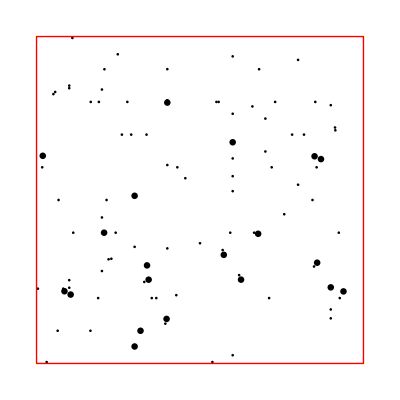

```mathematica
displayParticles[positions, radii, size]
```

### Cycle

```mathematica
packingFraction
```

0.449377

```mathematica
positions=positions+velocities(gtime-lastupdates);
```

```mathematica
radii=radii(1+gtime rate);
```

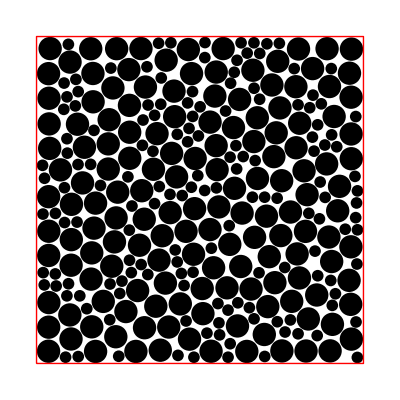

```mathematica
displayParticles[positions, radii, size]
```

```mathematica
overlapQ
```

True

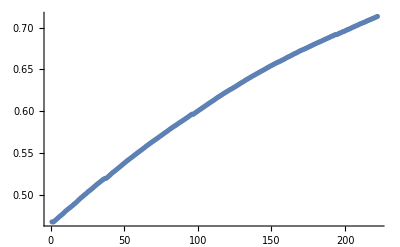

```mathematica
pf//ListPlot
```

```mathematica
Do[nevents=0;
(Process[];)//AbsoluteTiming, 10]
```

negative time{∞,0.0249836,-3.9106×10^-7,∞}{1,13}

False

$Aborted

```mathematica
nrows
```

14

```mathematica
nevents
```

6001

```mathematica
gtime
```

0.502822

```mathematica
ncollisions
```

7588

```mathematica
nevents
```

3001

```mathematica
gtime
```

0

```mathematica
positionsz=positions+velocities(gtime - lastupdates);
positionsz[[51]]
```

{0.604722,0.537269}

```mathematica
lastupdates[[49]]
```

```mathematica
positions[]
```

0.17811

```mathematica
For[i=1, i<n, i++,
For[j=i+1, j≤n, j++,
If[!overlapC[{positionsz⟦i⟧, radii⟦i⟧}, {positionsz⟦j⟧, radii⟦j⟧}],
Print[i," ", j]
]
]
]
```

```mathematica
overlapQ
```

False

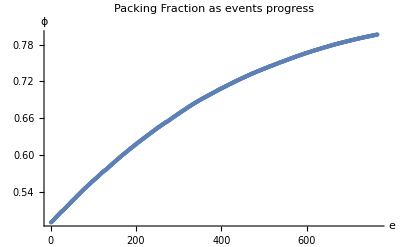

```mathematica
ListPlot[pf, PlotLabel->"Packing Fraction as events progress", AxesLabel->{"e", "ϕ"}]
```

```mathematica
pf//Length
```

19

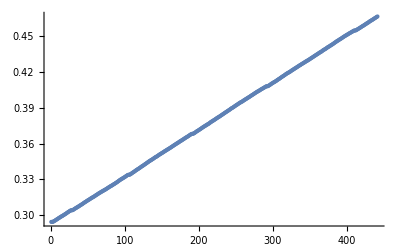

```mathematica
ListPlot@pf
```

9

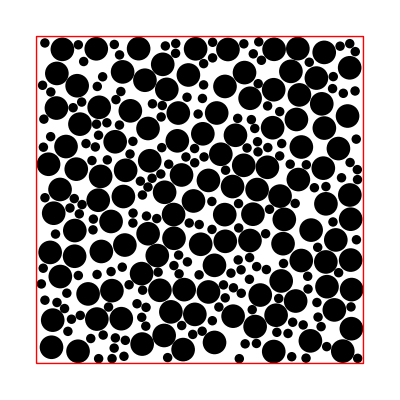

```mathematica
nrows
```

```mathematica
overlapQ
```

False

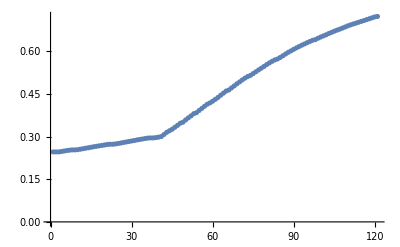

```mathematica
pf//ListPlot
```

### Test 1: 0.4, .4

```mathematica
Manipulate[displayParticles[nestpositions⟦i⟧,nestradii⟦i⟧, size], {i, 1, nestpositions//Length, 1}]
```

Part::partd: Part specification nestpositions⟦761⟧ is longer than depth of object.

Part::partd: Part specification nestradii⟦761⟧ is longer than depth of object.

Part::partd: Part specification nestpositions⟦761⟧ is longer than depth of object.

Part::partd: Part specification nestradii⟦761⟧ is longer than depth of object.

Riffle::list: List expected at position 1 in Riffle[nestpositions⟦761⟧,nestradii⟦761⟧].

Riffle::argtu: Riffle called with 1 argument; 2 or 3 arguments are expected.

```mathematica
positions//Length
```

300

```mathematica
nestpositions
```

```mathematica
pos2={{{{{0.5432533911815547,0.28922018188711585},{0.3866977000365339,0.3625726272978935},{0.526243462284669,0.14191144687696777},295,{0.8457176846655674,0.5327928975147314},{0.7525751808060925,0.4047239307441497}},220,{1}}}, {{{, , , , }}}};
```

```mathematica
rad2={{{{0.03162277660168379,0.03162277660168379,0.03162277660168379,0.03162277660168379,0.03162277660168379,290,0.012649110640673518,0.012649110640673518,0.012649110640673518,0.012649110640673518,0.012649110640673518},220,{1}}}, {{{, , , , }}}};
```

```mathematica
Export["mat1.dat", rad2]
```

mat1.dat

```mathematica
Export["mat2pos2.dat", pos2]
```

mat2pos2.dat

```mathematica
Manipulate[displayParticles[pos2⟦i⟧,rad2⟦i⟧, size], {i, 1, nestpositions//Length, 1}, SaveDefinitions->True]
```

rate = 0 to see collision error progress
small radii ratio
package everything